### Calcolo di S(R)

```mathematica
Clear["Global`*"]
```

#### SU(3)

```mathematica
Subscript[d, 3][p_,q_]:=(1/2)(p+1)(q+1)(p+q+2);
Subscript[c, 3][p_,q_]:=(1/3)(p^2+q^2+3p+3q+p q);
Subscript[su, 3][p_,q_]:=(Subscript[d, 3][p,q]Subscript[c, 3][p,q])/8;
Subscript[s, 3][k_]:=Piecewise[{{0,k==1 },{1/2,k==3},{5/2,k==6},{3,k==8},{35/2,k==15},{27,k==27}},k]; (*Causa complessità di esprimere tutto in funzione di d, ho definito una funzione appositamente per le particelle che ci interessano*)
```

#### SU(2)

```mathematica
Subscript[s, 2][d_]:=(1/12)d(d-1)(d+1); (*d=2j+1*)
(2j+1)(j(j+1))/3/.j->(d-1)/2//FullSimplify (*Check formula precedente*);
```

#### U(1)

```mathematica
Subscript[s, 1][Y_]:=(3/5)Y^2;
```

### Contributo al coupling assumendo k=1/2 (Weyl)

```mathematica
F[Nc_,Nw_,Y_]:=(2/3) {Subscript[s, 3][Nc] Nw , Subscript[s, 2][Nw] Nc, Subscript[s, 1][Y]Nc Nw}; (*Funzione che calcola Δb di una data particella*)
particelle={ {1,5,0},{6,3,5/3},{15,2,5/6},{3,4,5/6},{3,2,5/6 },{27,1,0},{8,3,0},{8,1,0},{1,3,0},{1,1,0}};
Δb=Apply[F,particelle,{1}] (*Applico F a tutte le particelle*)
```

{{0,20/3,0},{5,8,20},{70/3,5,25/3},{4/3,10,10/3},{2/3,1,5/3},{18,0,0},{6,32/3,0},{2,0,0},{0,4/3,0},{0,0,0}}

### Parametri

```mathematica
mZ=91.2; 
mX=14 10^3; (*Massa del quintupletto*)
Mgut=4 10^16;
α3=0.1173;
α2=0.033735;
α1=0.0169225;
bSM={-7,-19/6,41/10};
α={α3,α2,α1};
Δbχ={0,20/3,0}; (*Contributo al coupling del quintupletto*)
Δbparticelle={ 2 {5,8,20},2 {70/3,5,25/3},2{4/3,10,10/3},2{2/3,1,5/3},{18,0,0},{6,32/3,0},{2,0,0},{0,4/3,0},{0,0,0}}; (*Il fattore 2 è per l'antiparticella*)
listaparticelle={{6,3,5/3},{15,2,5/6},{3,4,5/6},{3,2,5/6 },{27,1,0},{8,3,0},{8,1,0},{1,3,0},{1,1,0}};



w[x_]:=1/(2Pi) Log[x]; (*Utile in seguito*)
r12=1/α1-1/α2; 
r23=1/α2-1/α3;
```

#### Soluzione con vincolo delle masse

```mathematica
choose={5,1,3,4,2,8}; (*Scegliere in ordine di massa. I numeri indicano la posizione della particella nell'array "listaparticelle" (5,1,3,4,2,8,7,6)*)
Print["Particelle scelte in ordine di massa crescente=", Table[listaparticelle[[choose[[i]]]],{i,1, Length[choose]}]]
Δbtot=Join[{bSM}, {Δbχ}, Table[Δbparticelle[[choose[[i]]]],{i,1,Length[choose]}]]; (*N+2*)
B1=Table[Δbtot[[i,3]],{i,1, Length[Δbtot]}]; (*N+2*)
B2=Table[Δbtot[[i,2]],{i,1, Length[Δbtot]}];
B3=Table[Δbtot[[i,1]],{i,1, Length[Δbtot]}];
B12=B1-B2; 
B23=B2-B3;
D12=Drop[B12,2]; (*N*)
D23=Drop[B23,2];
masse={Subscript[M, 1],Subscript[M, 3],(25 V Subscript[c, 1])/24+25/144 V ϵ Subscript[c, 3]+(3 Subscript[M, 1])/2,(25 V Subscript[c, 1])/24+25/144 V ϵ Subscript[c, 3]+(12 Subscript[M, 1])/7,(25 V Subscript[c, 1])/24+25/144 V ϵ Subscript[c, 3]+2 Subscript[M, 1],(25 V Subscript[c, 1])/21+(4199 V ϵ Subscript[c, 3])/21252+1/7 (13 Subscript[M, 1]-2 Subscript[M, 3]),(125 V Subscript[c, 1])/84+125/504 V ϵ Subscript[c, 3]+1/28 (73 Subscript[M, 1]-10 Subscript[M, 3]),(25 V Subscript[c, 1])/12+25/72 V ϵ Subscript[c, 3]+1/4 (13 Subscript[M, 1]-2 Subscript[M, 3])}(*8 (E'stato escluso il singoletto)*);
```

Particelle scelte in ordine di massa crescente={{27,1,0},{6,3,5/3},{3,4,5/6},{3,2,5/6},{15,2,5/6},{1,3,0}}

```mathematica
l=Table[1,Length[B12]](*Creo un'array di lunghezza N+2 (N è il numero di particelle scelte) di soli 1*);
var={V,ϵ,Subscript[c, 1],Subscript[c, 3],vgut}; 
setvalues={Mgut(0.30),0.30,2.5,1,w[Mgut]}; (*Inserire valori di V,ϵ,c_(1,)Subscript[c, 3] e vgut \*)
cond=Table[var[[i]]->setvalues[[i]],{i,1,Length[var]}];
wmassch=w[Drop[masse,-(8-Length[choose])]]; (*N*)
eq1=vgut(l. B12)- wmassch.D12==r12+B12[[1]]w[mZ]+B12[[2]] w[mX]/.cond; (*eq1 e eq2 rappresentano le condizioni di unificazione*)
eq2=vgut(l. B23)- wmassch.D23==r23+B23[[1]]w[mZ]+B23[[2]] w[mX]/.cond;
constraint=(1/α[[3]]-vgut(B1.l)+B1. Join[{w[mZ],w[mX]},wmassch])>0/. cond; (*Condizione di positività di Subscript[α, GUT]*)
constraint2=masse[[Length[choose]]]<Mgut/.cond (*Condizione affinchè la massima massa scelta sia minori di Subscript[M, GUT]*);
```

SOLUZIONE NUMERICA

```mathematica
sol=FindRoot[{eq1,eq2},{{Subscript[M, 1],1},{Subscript[M, 3],1}}](*Trova numericamente la soluzione partendo dai valori iniziali di*)
```

{M_1→2.35151×10^11,M_3→1.59496×10^14}

```mathematica
massasingoletto=(25 V Subscript[c, 1])/21+25/126 V ϵ Subscript[c, 3]+2/7 (7 Subscript[M, 1]-Subscript[M, 3]);
massasingoletto/.cond/.sol
```

3.63835×10^16

#### Plot con vincolo di tutte le masse sotto a GUT e positività di α_GUT

```mathematica
set={10^8,10^14} ;(*Setta il range dei plot*)
```

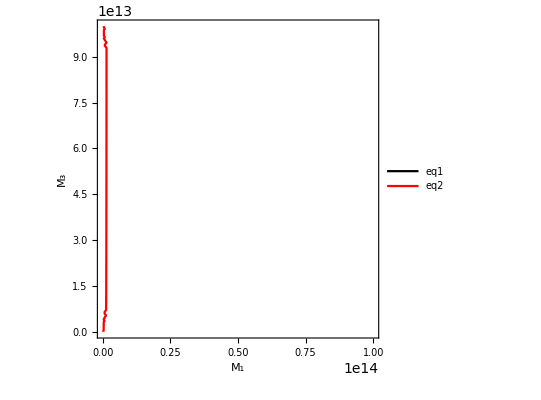

```mathematica
p1=RegionPlot[constraint && constraint2 && Subscript[M, 3]>Subscript[M, 1],{Subscript[M, 1],set[[1]],set[[2]]},{Subscript[M, 3],10^8,10^14},FrameLabel->{Subscript[M, 1],Subscript[M, 3]},PlotStyle->{Green,Opacity[0.05]}]; 
h=vgut(l. B12)- wmassch.D12-(r12+B12[[1]]w[mZ]+B12[[2]] w[mX])/.cond(*eq1*);
g=vgut(l. B23)- wmassch.D23-(r23+B23[[1]]w[mZ]+B23[[2]] w[mX])/.cond(*eq2*);
p2=ContourPlot[{h==0,g==0},{Subscript[M, 1],set[[1]],set[[2]]},{Subscript[M, 3],set[[1]],set[[2]]},ContourStyle->{Black,Red},PlotLegends->{"eq1","eq2"}];
Show[p1,p2]
```

#### Plot con vincolo di positività di α_GUT

```mathematica
pl1=RegionPlot[constraint && Subscript[M, 3]>Subscript[M, 1],{Subscript[M, 1],set[[1]],set[[2]]},{Subscript[M, 3],set[[1]],set[[2]]},FrameLabel->{Subscript[M, 1],Subscript[M, 3]},PlotStyle->{Green,Opacity[0.05]}];
h=vgut(l. B12)- wmassch.D12-(r12+B12[[1]]w[mZ]+B12[[2]] w[mX])/.cond;
g=vgut(l. B23)- wmassch.D23-(r23+B23[[1]]w[mZ]+B23[[2]] w[mX])/.cond;
pl2=ContourPlot[{h==0,g==0},{Subscript[M, 1],set[[1]],set[[2]]},{Subscript[M, 3],set[[1]],set[[2]]},ContourStyle->{Black,Red},PlotLegends->{"eq1","eq2"}];
Show[pl1,pl2]
```

-Graphics-

#### Plot finale

Massa delle particelle={2.35151×10^11,1.59496×10^14,3.18754×10^16,3.18754×10^16,3.18755×10^16,3.63804×10^16,4.54794×10^16,6.3671×10^16}

{91.2,14000,2.35151×10^11,1.59496×10^14,3.18754×10^16,3.18754×10^16,3.18755×10^16,3.63804×10^16,40000000000000000}

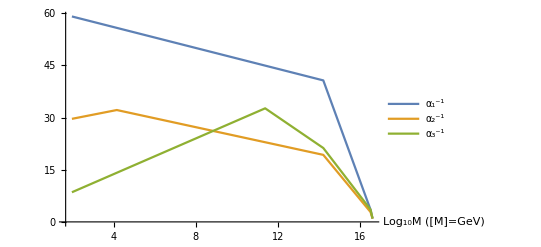

1/α_GUT=0.958547

```mathematica
Print["Massa delle particelle=",masse/.cond  /.sol];
massdrop=NumericalSort[Join[{mZ,mX,Mgut},Drop[masse/.cond  /.sol,-(8-Length[choose])]]] (*N+3*)
list1=Table[ 1/α[[3]]-Sum[(Δbtot[[i,3]])/(2Pi)Log[massdrop[[j]]/massdrop[[i]]],{i,1,j-1}],{j,1,Length[massdrop]}];(*N+2*)
list2=Table[ 1/α[[2]]-Sum[(Δbtot[[i,2]])/(2Pi)Log[massdrop[[j]]/massdrop[[i]]],{i,1,j-1}],{j,1,Length[massdrop]}];  
list3=Table[ 1/α[[1]]-Sum[(Δbtot[[i,1]])/(2Pi)Log[massdrop[[j]]/massdrop[[i]]],{i,1,j-1}],{j,1,Length[massdrop]}]; 
plot1=Table[{Log10[massdrop[[i]]],list1[[i]]},{i,1,Length[massdrop]}];
plot2=Table[{Log10[massdrop[[i]]],list2[[i]]},{i,1,Length[massdrop]}];
plot3=Table[{Log10[massdrop[[i]]],list3[[i]]},{i,1,Length[massdrop]}];
ListLinePlot[{plot1,plot2,plot3},PlotRange->All,PlotLegends->{"α_1^-1","α_2^-1","α_3^-1"},AxesLabel->{"Log_10M ([M]=GeV)"}]
Print["1/α_GUT=",Last[list1]]
```

### Soluzione Running Coupling

```mathematica
sol3=DSolve[{x y'[x]==(b/(16Pi^2)) y[x]^3,y[M0]==y0},y[x],x] //Simplify;
1/((y[x]/.sol3[[2]])^2/(4Pi))
```

((8 π^2)/y0^2+b Log[M0]-b Log[x])/(2 π)

## Soluzione approssimata

#### Parametri teoria

```mathematica
Λgut=  4 10^(16);
```

#### Equazioni sistema

```mathematica
eqz1=((Log[vgut])/(2Pi))(l. B12)- wmassch.D12-(r12+B12[[1]]w[mZ]+B12[[2]] w[mX])/. V->ϵ vgut;
eqz2=((Log[vgut])/(2Pi))(l. B23)- wmassch.D23-(r23+B23[[1]]w[mZ]+B23[[2]] w[mX])/.V->ϵ vgut;
```

### Soluzione per M_3

```mathematica
Series[eqz1/.Subscript[M, 1]->0,{Subscript[M, 3],0,0},{ϵ,0,1}]//FullSimplify
```

((-24.4685+2.85418 Log[vgut]+1.06103 Log[vgut ϵ c_1]-3.81972 Log[M_3])+(0.176691 c_3 ϵ)/c_1+O[ϵ]^2)+O[M_3]^1

```mathematica
Solve[(-24.468451873183994+2.8541786461146565 Log[vgut]+1.0610329539459689 Log[vgut ϵ Subscript[c, 1]]-3.8197186342054885 Log[Subscript[M, 3]])+(0.17669064450730804 Subscript[c, 3] ϵ)/Subscript[c, 1]==0,Subscript[M, 3]]
```

{{M_3→0.00165191 ⅇ^((0.0462575 ϵ c_3)/c_1) vgut^1.025 ϵ^0.277777777777778 c_1^0.277777777777778}}

```mathematica
Solve[(-23.222427102078985+1.1565259198011062 Log[vgut]+2.7586856802595188 Log[vgut ϵ Subscript[c, 1]]-3.8197186342054885 Log[Subscript[M, 3]])+(0.4596327655595664 Subscript[c, 3] ϵ)/Subscript[c, 1]==0,Subscript[M, 3]]
```

{{M_3→0.00228905 ⅇ^((0.120332 ϵ c_3)/c_1) vgut^1.025 ϵ^0.722222222222222 c_1^0.722222222222222}}

#### Soluzione per M_1

```mathematica
PowerExpand[Series[eqz2,{Subscript[M, 1],0,0},{Subscript[M, 3],0,0},{ϵ,0,0}]/. Out[300][[1]]]//FullSimplify
```

ReplaceAll::reps: {300} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(((-33.9162-0.238732 Log[vgut]+2.75869 Log[ϵ]+2.75869 Log[c_1]+2.86479 Log[M_1]-0.95493 Log[M_3])+O[ϵ]^1)+O[M_3]^1)+O[M_1]^1/.300

```mathematica
Solve[(-27.799133505652037-1.2175353146529988 Log[vgut]+2.4934274417730276 Log[ϵ]+2.4934274417730276 Log[Subscript[c, 1]]+2.8647889756541165 Log[Subscript[M, 1]])==0,Subscript[M, 1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{M_1→16378.6 (vgut^0.425/(ϵ^0.87037 c_1^0.87037))^1.}}

```mathematica
solution1=Solve[(-28.529248330547443-1.2175353146529986 Log[vgut]+1.6446010786162524 Log[ϵ]+1.6446010786162524 Log[Subscript[c, 1]]+2.8647889756541165 Log[Subscript[M, 1]])+(0.2742854062073172 Subscript[c, 3] ϵ)/Subscript[c, 1]==0,Subscript[M, 1]];
solution1
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{M_1→21132.9 ((ⅇ^(-(0.0957437 ϵ c_3)/c_1) vgut^0.425)/(ϵ^0.574074 c_1^0.574074))^1.}}

### Soluzione per α_gut

```mathematica
(1/α[[3]]-vgut(B1.l)+B1. Join[{w[mZ],w[mX]},wmassch])
```

62.0379-(2123 vgut)/30+(10 Log[(25 V c_1)/24+25/144 V ϵ c_3+(3 M_1)/2])/(3 π)+(5 Log[(25 V c_1)/24+25/144 V ϵ c_3+(12 M_1)/7])/(3 π)+(25 Log[(25 V c_1)/24+25/144 V ϵ c_3+2 M_1])/(3 π)+(20 Log[M_3])/π

```mathematica
αGUT=(1/α[[3]]-(Log[vgut]/(2Pi))(B1.l)+B1. Join[{w[mZ],w[mX]},wmassch])/. V-> ϵ vgut
```

62.0379-(2123 Log[vgut])/(60 π)+(10 Log[25/24 vgut ϵ c_1+25/144 vgut ϵ^2 c_3+(3 M_1)/2])/(3 π)+(5 Log[25/24 vgut ϵ c_1+25/144 vgut ϵ^2 c_3+(12 M_1)/7])/(3 π)+(25 Log[25/24 vgut ϵ c_1+25/144 vgut ϵ^2 c_3+2 M_1])/(3 π)+(20 Log[M_3])/π

```mathematica
PowerExpand[Series[αGUT,{Subscript[M, 1],0,0},{Subscript[M, 3],0,0},{ϵ,0,1}]/.Out[270][[1]]]//FullSimplify
```

ReplaceAll::reps: {270} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(((62.2111-7.01873 Log[vgut]+4.24413 Log[ϵ]+4.24413 Log[c_1]+6.3662 Log[M_3])+(0.707355 c_3 ϵ)/c_1+O[ϵ]^2)+O[M_3]^1)+O[M_1]^1/.270

```mathematica
Solve[(21.430351906943258-0.4933803235848763 Log[vgut]+6.012520072360489 Log[ϵ]+6.012520072360489 Log[Subscript[c, 1]])+(1.0018397101428258 Subscript[c, 3] ϵ)/Subscript[c, 1]==0, vgut]
```

{{vgut→7.30993×10^18 ⅇ^((2.03056 ϵ c_3)/c_1) ϵ^12.1863799283154 c_1^12.1863799283154}}

```mathematica
asolu=(21.430351906943258-0.4933803235848763 Log[vgut]+6.012520072360489 Log[ϵ]+6.012520072360489 Log[Subscript[c, 1]])+(1.0018397101428258 Subscript[c, 3] ϵ)/Subscript[c, 1];
```

### Soluzioni con c_3 uguale a 0

```mathematica
M3sol=Out[100][[1]]/. Subscript[c, 3]->0
M1sol=Out[104][[1]]/.Subscript[c, 3]->0
asold=Out[111][[1]]/.Subscript[c, 3]->0
```

{M_3→0.00165191 vgut^1.025 ϵ^0.277777777777778 c_1^0.277777777777778}

{M_1→16378.6 (vgut^0.425/(ϵ^0.87037 c_1^0.87037))^1.}

{vgut→7.30993×10^18 ϵ^12.1863799283154 c_1^12.1863799283154}

```mathematica
asolcond=asolu/.Subscript[c, 3]->0
```

21.4304-0.49338 Log[vgut]+6.01252 Log[ϵ]+6.01252 Log[c_1]

### Decadimento del protone

```mathematica
protondecay=ϵ>(10^(16))/(Λgut)
```

ϵ>1/4

### Positività di α_gut

```mathematica
positivitàdigut= Λgut<vgut/.asold
```

40000000000000000<7.30993×10^18 ϵ^12.1863799283154 c_1^12.1863799283154

{vgut→7.30993×10^18 ϵ^12.1863799283154 c_1^12.1863799283154}

### Bound c_2

```mathematica
boundc2=0.1< Subscript[c, 1]/ϵ < 10;
```

### Bound c_5

```mathematica
boundc5=0.1< 3( Subscript[M, 3]/(Λgut ϵ^2))<10/. {M3sol[[1]]} /. vgut->Λgut
```

0.1<(0.0128872 c_1^0.277777777777778)/ϵ^1.722222222222222<10

#### Bound neutrini

```mathematica
boundneutrini=ϵ< (Λgut)/(10^(14))Subscript[c, 1];
```

#### Bound massa

```mathematica
boundmassa=Subscript[c, 1] ϵ<12/25 ;
boundmassa11= Subscript[c, 1] ϵ< 21/25;
```

#### Bound 27 (Occhio se BBN o QCD)

```mathematica
Γ=Subscript[M, 1](Subscript[M, 1]/Λgut)^4 /(((16Pi^2)^2) 2(49152 Pi^5))/. {M1sol[[1]]}/. {ϵ->1};
decadimentodella27= Γ>6.6 10^(-25) (*Con 25 ci riferiamo solo alla BBN, con 20 alla QCD*)
```

6.13731×10^-58 (vgut^0.425/c_1^0.87037)^5.>6.6×10^-25

```mathematica
Subscript[M, 1](Subscript[M, 1]/Λgut)^4 /(((16Pi^2)^2) 2(49152 Pi^5))/. Subscript[M, 1]->2.35 10^11

cond2=vgut<asold[[1]]/. ϵ->1
```

3.73198×10^-22

vgut<(vgut→7.30993×10^18 c_1^12.1863799283154)

```mathematica
decadimentodella27
```

6.13731×10^-58 (vgut^0.425/c_1^0.87037)^5.>6.6×10^-25

### Plot vari

```mathematica
RegionPlot[{decadimentodella27 },{vgut, 10^(16), 10^(18)},{Subscript[c, 1],0,18},FrameLabel->{Λ,Subscript[c, 1] ϵ}]
```

-Graphics-

```mathematica
RegionPlot[{decadimentodella27 ,vgut<7.309929002947738*^18 Subscript[c, 1]^(12.1863799283153895203213323839008808136`15.954589770191005)},{vgut,4 10^(16), 10^(18)},{Subscript[c, 1],0,18}]
```

-Graphics-

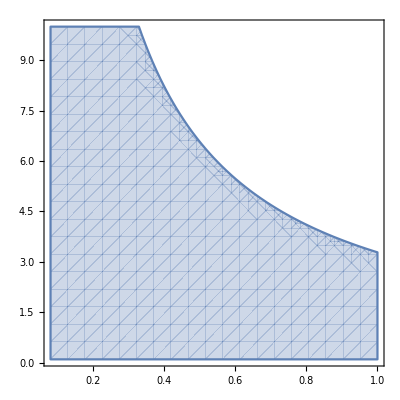

```mathematica
RegionPlot[ {decadimentodella27},{ϵ,1/(4Pi),1},{Subscript[c, 1],0.1,10}] (*Plot a Lambda fissato, solo il bound dovuto alla 27 impone questo*)
```

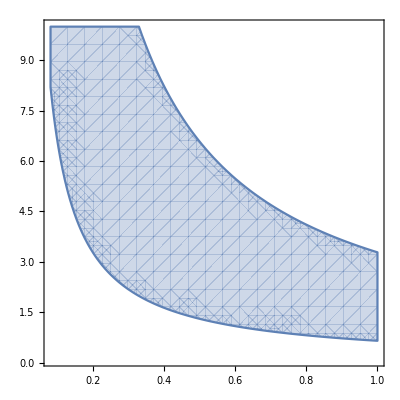

```mathematica
RegionPlot[{decadimentodella27 && positivitàdigut },{ϵ,1/(4Pi),1},{Subscript[c, 1],0.1,10}]
```

#### Tutto insieme

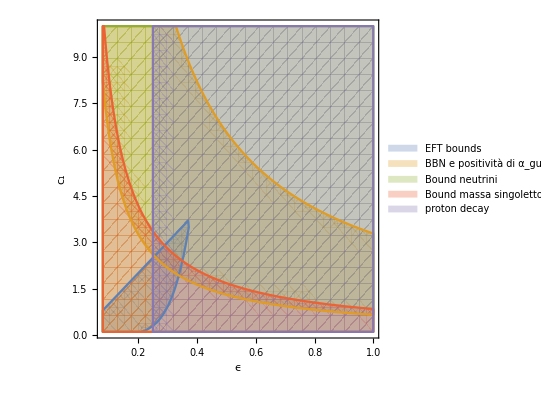

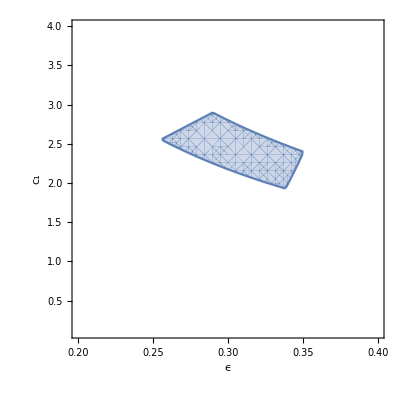

```mathematica
RegionPlot[{{boundc5 && boundc2} ,{positivitàdigut && decadimentodella27} ,boundneutrini, boundmassa11 ,protondecay},{ϵ,1/(4Pi),1},{Subscript[c, 1],0.1,10},FrameLabel->{"ϵ","c_1"},PlotLegends->{"EFT bounds","BBN e positività di α_gut","Bound neutrini","Bound massa singoletto","proton decay"}]
RegionPlot[{boundc5 && boundc2 && positivitàdigut && decadimentodella27 && boundmassa11 && protondecay},{ϵ,0.2,0.4},{Subscript[c, 1],0.1,4},FrameLabel->{"ϵ","c_1"}]
```